```mathematica
SetOptions[$FrontEnd, "ClearEvaluationQueueOnKernelQuit" -> False]
```

## NicePlots

```mathematica
Quit[];
```

```mathematica
testName = First@NotebookRead[PreviousCell[CellStyle -> "Section"]];
```

```mathematica
testFileName=FileNameJoin[{DirectoryName[NotebookDirectory[],1],testName<>".wlt"}];
pacletDir=DirectoryName[testFileName,2];
PacletDirectoryLoad[pacletDir];
testContextBase=FileBaseName[testFileName];
$ContextPath=Cases[$ContextPath,Except["PacletizedResourceFunctions`"]];
```

```mathematica
Needs["FernandoDuarte`LongRunRisk`"];
```

```mathematica
model=Models["NRC"];
```

```mathematica
momF =UncondE;
var = nombondyield[t,m];
maxMaturity=24;
varF=momF@var
```

UncondE[nombondyield[t,m]]

```mathematica
solWc=FernandoDuarte`LongRunRisk`ComputationalEngine`SolveEulerEq`updateCoeffs[model,"UpdatePd"->True];
```

```mathematica
ToNum["Rules",model];
```

```mathematica
ToNum["Rules",model,"MaxMaturity"->1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
ReleaseHold@If[KeyExistsQ[model["extraInfo"],"initialGuess"],"initialGuess"->model["extraInfo"]["initialGuess"],Hold@Sequence[] ]
```

initialGuess→<|Ewc→{4.6},Epd→{{4.7},{6},{7}}|>

```mathematica
FernandoDuarte`LongRunRisk`Tools`ToNumber`Private`toNumRules[model,"MaxMaturity"->1,{}]
```

```mathematica
FernandoDuarte`LongRunRisk`Tools`ToNumber`Private`toNumRules[model,"MaxMaturity"->1,{} ,"initialGuess"-><|"Ewc"->{4.6},"Epd"->{{0,15},{0,15},{5.5}}|>]
```

{A[0]→4.59417,A[1]→-0.124759,A[2]→-0.0991435,A[3]→-0.000090171,A[4]→1.22397,A[5]→-26.0718,B[1][0]→4.72804,B[1][1]→3.54114,B[1][2]→-0.208473,B[1][3]→0.00256262,B[1][4]→94.143,B[1][5]→10.5824,B[2][0]→6.27158,B[2][1]→3.58307,B[2][2]→0.20738,B[2][3]→0.00261096,B[2][4]→-1.75389,B[2][5]→-72.3573,B[3][0]→5.50617,B[3][1]→-1.02122,B[3][2]→0.293319,B[3][3]→-0.000742548,B[3][4]→-19.1369,B[3][5]→-111.316,R[0][0]→0.,R[0][4]→0.,R[0][5]→0.,R[0][1]→0,R[0][2]→0,R[0][3]→0,R[1][0]→-0.00998022,R[1][4]→-0.0161127,R[1][5]→0.468326,R[1][1]→0.0260533,R[1][2]→0.0991435,R[1][3]→-5.54456×10^-19,P[0][0]→0.,P[0][4]→0.,P[0][5]→0.,P[0][1]→0,P[0][2]→0,P[0][3]→0,P[1][0]→-0.0133116,P[1][4]→-0.00910375,P[1][5]→0.468326,P[1][1]→-0.773117,P[1][2]→0.0991435,P[1][3]→-0.00073007,delta→0.99,Esg→-0.00624,gamma→15,muc→0.0016426,mup→0.00327532,phic→0.00204654,phig→0.00292724,phip→-0.0024624,psi→2,rhocp→-0.0521066,rhog→0.996289,rhop→0.79917,theta→(1-gamma)/(1-1/psi),xic→-0.198287,xip→0.00073007,mud[1]→0.000171799,mud[2]→0.0059643,mud[3]→0.000344067,phidc[1]→0.0337002,phidc[2]→-0.0516542,phidc[3]→0.0318068,rhodp[1]→0.709922,rhodp[2]→0.698934,rhodp[3]→-0.234447,xid[1]→-0.307616,xid[2]→0.108237,xid[3]→0.194176,Ewc→4.59417,Epd[FernandoDuarte`LongRunRisk`Tools`ToNumber`Private`ind$_]:>(B[FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`j][0]/.FernandoDuarte`LongRunRisk`Model`ProcessModels`Private`j→FernandoDuarte`LongRunRisk`Tools`ToNumber`Private`ind$/.{A[0]→4.59417,A[1]→-0.124759,A[2]→-0.0991435,A[3]→-0.000090171,A[4]→1.22397,A[5]→-26.0718,B[1][0]→4.72804,B[1][1]→3.54114,B[1][2]→-0.208473,B[1][3]→0.00256262,B[1][4]→94.143,B[1][5]→10.5824,B[2][0]→6.27158,B[2][1]→3.58307,B[2][2]→0.20738,B[2][3]→0.00261096,B[2][4]→-1.75389,B[2][5]→-72.3573,B[3][0]→5.50617,B[3][1]→-1.02122,B[3][2]→0.293319,B[3][3]→-0.000742548,B[3][4]→-19.1369,B[3][5]→-111.316,R[0][0]→0.,R[0][4]→0.,R[0][5]→0.,R[0][1]→0,R[0][2]→0,R[0][3]→0,R[1][0]→-0.00998022,R[1][4]→-0.0161127,R[1][5]→0.468326,R[1][1]→0.0260533,R[1][2]→0.0991435,R[1][3]→-5.54456×10^-19,P[0][0]→0.,P[0][4]→0.,P[0][5]→0.,P[0][1]→0,P[0][2]→0,P[0][3]→0,P[1][0]→-0.0133116,P[1][4]→-0.00910375,P[1][5]→0.468326,P[1][1]→-0.773117,P[1][2]→0.0991435,P[1][3]→-0.00073007}//.{delta→0.99,Esg→-0.00624,gamma→15,muc→0.0016426,mup→0.00327532,phic→0.00204654,phig→0.00292724,phip→-0.0024624,psi→2,rhocp→-0.0521066,rhog→0.996289,rhop→0.79917,theta→(1-gamma)/(1-1/psi),xic→-0.198287,xip→0.00073007,mud[1]→0.000171799,mud[2]→0.0059643,mud[3]→0.000344067,phidc[1]→0.0337002,phidc[2]→-0.0516542,phidc[3]→0.0318068,rhodp[1]→0.709922,rhodp[2]→0.698934,rhodp[3]→-0.234447,xid[1]→-0.307616,xid[2]→0.108237,xid[3]→0.194176})}

```mathematica
dataF=Table[{m,varF}/.m->mm,{mm,maxMaturity}]//ToNum[model,{},solWc,"MaxMaturity"->24,"UpdateBonds"->True]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{1,0.00857922},{2,0.00830778},{3,0.00814227},{4,0.00799844},{5,0.00785977},{6,0.0077209},{7,0.00757964},{8,0.00743495},{9,0.00728627},{10,0.00713326},{11,0.0069757},{12,0.00681341},{13,0.00664627},{14,0.00647415},{15,0.00629691},{16,0.00611444},{17,0.00592661},{18,0.00573328},{19,0.00553431},{20,0.00532956},{21,0.00511888},{22,0.00490209},{23,0.00467903},{24,0.00444952}}

```mathematica
Dynamic
```

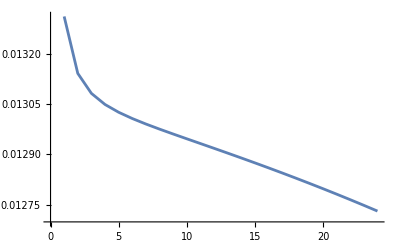

```mathematica
ListLinePlot[dataF]
```

```mathematica
paramNumRange=<|
	alpha->{0.005,0.15,0.01},
	tau->{0.1,4,0.05},
	beta->{0.001,0.1,0.005},
	av->{0.01,0.15,0.01},
	gamma->{1,10,0.5},
	kappa->{0.1,2,0.1},
	muG->{-1,1,0.1},
	kappaG->{0.01,2,0.1},
	sigmaG->{-0.3,0.3,0.001},
	X0->{1,10000,250},
	g0->{-5,5,0.2},
	z0->{-5,5,1},
	varepsilon->{1,3,0.25},
	phi0->{-0.1,0.5,0.005},
	phig->{-0.2,0.2,0.005},
	phiz->{-0.2,0.2,0.005},
	gmin->{-2,2,0.1},
	gmax->{-2,6,0.1},
	T->{1,5,1}
|>;
```

```mathematica
toParamRange=Map[{#[[1]],#[[2]],(#[[2]]-#[[1]])/20}&,Flatten/@((N@(toParam//.toParam/.Map[Interval@Most@#&,paramNumRange]))/.Interval[x_]->List[x])];
paramRange=Join[paramNumRange,toParamRange];

paramDyn={phig,phi0,muG,sigmaG,kappaG,alpha,tau,beta,av,gmin,gmax};
paramDynAssoc=param[[Key[#]&/@paramDyn]];





varNamesTeXAssoc=(Association@Thread[varNames->varNamesTeX]);
irfControls={
{{gminIRF,-0.5,"gminIRF"},-6,3,0.1,Appearance->{"Open",Small}},
{{gmaxIRF,0.12,"gmaxIRF"},-3,6,0.1,Appearance->{"Open",Small}},
{{g0min,-0.15,"g0minIRF"},-6,6,0.1,Appearance->{"Open",Small}},
{{g0med,0.09,"g0medIRF"},-6,6,0.1,Appearance->{"Open",Small}},
{{g0max,0.11,"g0maxIRF"},-6,6,0.1,Appearance->{"Open",Small}}
};

paramStatControls=KeyValueMap[{{ToExpression[ToString[#1]<>"M"],#2,ToString[#1]},paramRange[#1]/.List->Sequence,Appearance -> {"Open",Small}}&,paramDynAssoc];

parControls=Join[paramStatControls,irfControls];
```

```mathematica
SetOptions[$FrontEnd, "ClearEvaluationQueueOnKernelQuit" -> True]
```

```mathematica
Manipulate[

,

Evaluate[Sequence@@parControls]
,
ContinuousAction->None
]
```